```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

## Constants definitions

```mathematica
g=9.81;
r=53/2*10^(-3);
e=12*10^(-3);
m=0.375;
J3=0.000055;
J1=0.000055;
h=31.25*10^(-3);
x0 = 2.5*10^(-2);
```

## Solving equations for the gyroscope with forced motion

```mathematica
EquationForced = {
(J1 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-J1 D[θ[t],{t, 2}]-J3 Sin[θ[t]] D[ϕ[t],t] D[ψ[t],t]-(J3 Sin[2 θ[t]] (D[ϕ[t],t])^2)/2+g h m Sin[θ[t]]+(h^2 m Sin[2 θ[t]] (D[ϕ[t],t])^2)/2-h^2 m D[θ[t],{t, 2}]+h m w^2 x0 Sin[t w] Sin[ϕ[t]] Cos[θ[t]]==0,
-J1 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-J1 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+J3 Sin[θ[t]]^2 D[ϕ[t],{t, 2}]+J3 Sin[θ[t]] D[ψ[t],t] D[θ[t],t]+J3 Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]-J3 Cos[θ[t]] D[ψ[t],{t, 2}]-J3 D[ϕ[t],{t, 2}]-h^2 m Sin[θ[t]]^2 D[ϕ[t],{t, 2}]-h^2 m Sin[2 θ[t]] D[ϕ[t],t] D[θ[t],t]+h m w^2 x0 Sin[t w] Sin[θ[t]] Cos[ϕ[t]]==0,
J3 (Sin[θ[t]] D[ϕ[t],t] D[θ[t],t]-Cos[θ[t]] D[ϕ[t],{t, 2}]-D[ψ[t],{t, 2}])==0,
θ[0] == Pi/6,
ϕ[0] == 0, 
ψ[0] == 0, 
θ'[0] == 0,
ϕ'[0] ==0 , 
ψ'[0] ==  2Pi * hz
};
```

```mathematica
SolutionForced = Flatten@NDSolve[EquationForced /. {w ->2*Pi*0.535, hz -> 100 }, {θ[t], ϕ[t], ψ[t]}, {t, 0, 300}];
```

```mathematica
θForced[t_] = 180/Pi*θ[t]/. SolutionForced;
ϕForced[t_] = 180/Pi*ϕ[t]/. SolutionForced;
ψForced[t_] = 180/Pi*ψ[t]/. SolutionForced;
```

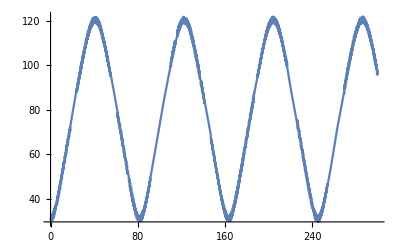

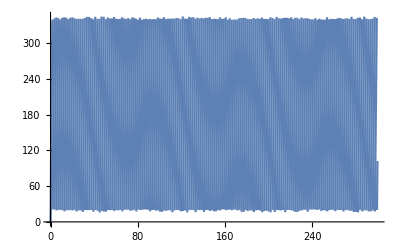

```mathematica
Plot[Mod[θForced[t], 360], {t, 0, 300}, ImageSize->"Large"]
Plot[Mod[ϕForced[t], 360], {t, 0, 300}, ImageSize->"Large"]
```

## Finding the resonant frequency

```mathematica
Listω = Range[2*Pi*0.5,2*Pi*0.6, 0.1];
```

```mathematica
Subscript[Listθ, max] = Table[Table[NMaximize[(θ[t]/. (Flatten@NDSolve[EquationForced /. {w ->k, hz -> n}, {θ[t], ϕ[t], ψ[t]}, {t, 0., 300.}])), {t, 0., 100.}, Method->"DifferentialEvolution"][[1]],
{k, 2*Pi*0.5,2*Pi*0.6, 0.1}], {n, 100, 200, 0.3}];
```

$Aborted

```mathematica
Subscript[Coupleωθ, max]= Transpose[{Listω, Subscript[Listθ, max]}]
```

{{3.14159,0.867769},{3.24159,1.07594},{3.34159,2.38096},{3.44159,1.35711},{3.54159,0.593277},{3.64159,0.568702},{3.74159,0.568685}}

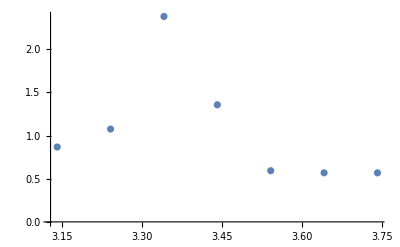

```mathematica
ListPlot[Subscript[Coupleωθ, max]]
```

```mathematica
Subscript[Listθ, max]
```

{0.867769,1.07594,2.38096,1.35711,0.593277,0.568702,0.568685}